# Zapori v Evropki uniji

Datum : 23. 3. 2021

## Podatki, ki jih bomo uporabili:

```mathematica
drzaveEvropa = CountryData["Europe", "Name"](*Vse evropske države.*);
```

```mathematica
drzaveEU = CountryData["EU", "Name"] (*Vse države Evropske Unije.*);
```

```mathematica
flags = {}
```

{}

```mathematica
For[i=0,i<Length[drzaveEvropa],i++; AppendTo[flags,CountryData[drzaveEvropa[[i]],"Flag"]]];
```

```mathematica
flags;
```

```mathematica
steviloZapornikovEvropa = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\persons_held_total.xlsx"][[1]];
```

```mathematica
evropskeDrzaveZaporniki = Select[steviloZapornikovEvropa, #[[1]]=="Europe"&];
popolniPodatkiEvropa = Select[evropskeDrzaveZaporniki, !MemberQ[#,""]&](*Vrstice z vsemi podatki*);
```

```mathematica
DrzaveJuznaEvropa = {}
```

```mathematica
DrzaveVzhodnaEvropa = {}
```

```mathematica
DrzaveSevernaEvropa = {}
```

```mathematica
Države in relativne vrednosti zapornikov med 2003-2018:
```

```mathematica
steviloZapornikovEvropaRel = Select[popolniPodatkiEvropa][[1]];
(*[[6;;-1;;2]]*)
Length[steviloZapornikovEvropaRel];
```

```mathematica
SeznamDrzavInVrednosti = {};
```

```mathematica
(*Seznam držav in relativne vrednosti zapornikov med leti 2003 in 2018 npr. {{drzava,vrednost_1, vrednost_2,..., vrednost_n}{...}{...}*)
```

```mathematica
For[i=0, i<Length[steviloZapornikovEvropaRel], i++;AppendTo[SeznamDrzavInVrednosti, Flatten[{steviloZapornikovEvropaRel[[i]][[3]],steviloZapornikovEvropaRel[[i]][[6;;-1;;2]]}]]];
```

```mathematica
SeznamDrzavInVrednosti;
```

```mathematica
(*Seznam časovnih vrst za relativno število zapornikov med leti 2003 in 2018 v Evropskih državah*)
```

```mathematica
SeznamCasovnihVrst = {};
```

```mathematica
For[i=0,i<Length[SeznamDrzavInVrednosti],i++;
AppendTo[SeznamCasovnihVrst,TimeSeries[SeznamDrzavInVrednosti[[i]][[2;;-1]],{Range[2003, 2018]}]]]
```

```mathematica
SeznamCasovnihVrst;
```

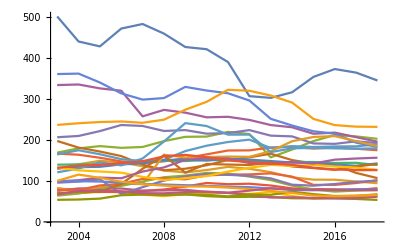

```mathematica
ListLinePlot[SeznamCasovnihVrst,ImageSize->Full]
```

```mathematica
(*ListLinePlot[popolniPodatkiEvropa,PlotLabel->"Število zaprtih oseb v Evropi med leti 2003 in 2018 - Relativno",ImageSize->Large,PlotTheme->"Detailed"]*)
```

```mathematica
steviloZapornikovAbs = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_absolutno.xlsx"][[1]];
```

```mathematica
jeVEU[x_]:= MemberQ[drzaveEU, CountryData[x]]; (*Funkcija preveri ali je država članica EU.*)
```

```mathematica
drzaveEUZaporniki =Select[steviloZapornikovAbs,MemberQ[drzaveEU, #[[1]]]&];
```

```mathematica
nekaj = Select[steviloZapornikovEvropa, #[[3]] == "Slovenia"&]
```

{{Europe,Southern Europe,Slovenia,UN-CTS,1070.,53.8,1085.,54.5,1132.,56.7,1301.,65.,1336.,66.4,1318.,65.2,1365.,67.1,1351.,66.1,1273.,62.1,1377.,66.9,1360.,65.9,1522.,73.6,1399.,67.6,1308.,63.1,1316.,63.4,1396.,67.2}}

```mathematica
zapornikiSlovenija0318ABS = Select[steviloZapornikovEvropa, #[[3]] == "Slovenia"&][[1]][[5;;-1;;2]];(*Seznam absolutnih vrednosti števila zapornikov med leti 2003 - 2018 v republiki Sloveniji.*)
```

```mathematica
zapornikiSlovenija0318Rel = Select[steviloZapornikovEvropa, #[[3]] == "Slovenia"&][[1]][[6;;-1;;2]];
(*Seznam relativnih vrednosti števila zapornikov na 100.000 prebivalcev v republiki Sloveniji.*)
```

```mathematica
zapornikiSlovenija = Select[steviloZapornikovAbs, #[[1]] == "Slovenia"&];
```

```mathematica
zapornikiSlovenija[[1]][[2;;Length[zapornikiSlovenija[[1]]]]]; (*Število zaprtih po letih v Slovenije med leti 2009 in 2018*)
```

```mathematica
zapornikiSlovenijaTS0318Rel = TimeSeries[zapornikiSlovenija0318Rel,{Range[2003, 2018]}];
```

```mathematica
zapornikiSlovenijaTS0318ABS = TimeSeries[zapornikiSlovenija0318ABS,{Range[2003, 2018]}];
(* Časovna vrsta absolutnega števila zapornikov v republiki Sloveniji med leti 2003 in 2018*)
```

```mathematica
(*zapornikiSlovenijaTS = TimeSeries[zapornikiSlovenija[[1]][[2;;Length[zapornikiSlovenija[[1]]]]], {Range[2009, 2018]}](*Časovna vrsta zaporniki Slovenija.*)*)
```

```mathematica
(*ListLinePlot[zapornikiSlovenijaTS, PlotLabel->Style["Število zaprtih oseb v Sloveniji med leti 2003 in 2018", 16, Darker[Blue], Background->Lighter[Yellow]], ImageSize->Large, PlotTheme->"Detailed"]*)
```

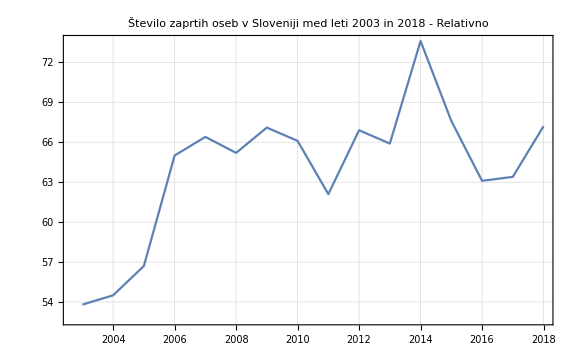

```mathematica
ListLinePlot[zapornikiSlovenijaTS0318Rel,PlotLabel->"Število zaprtih oseb v Sloveniji med leti 2003 in 2018 - Relativno",ImageSize->Large,PlotTheme->"Detailed"]
```

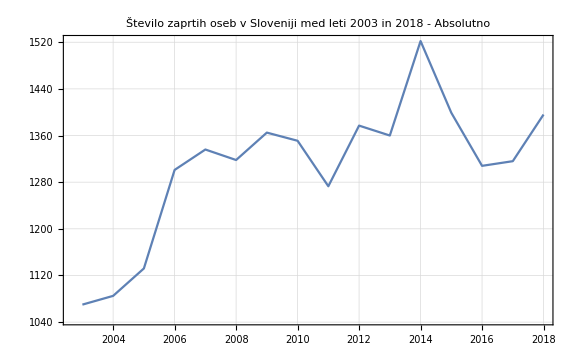

```mathematica
ListLinePlot[zapornikiSlovenijaTS0318ABS,PlotLabel->"Število zaprtih oseb v Sloveniji med leti 2003 in 2018 - Absolutno",ImageSize->Large,PlotTheme->"Detailed"]
```

```mathematica
s = steviloZapornikovAbs[[1]];
```

```mathematica
steviloZapornikovEU1 = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_po_drzavi.xlsx", {"Data", 5, Range[9, 51]}];
```

```mathematica
stZaprtiPoLetuEU = Select[steviloZapornikovEU, MemberQ[drzaveEU,#[[0]]]&]
```

Select::normal: Nonatomic expression expected at position 1 in Select[steviloZapornikovEU,MemberQ[drzaveEU,#1⟦0⟧]&].

Select[steviloZapornikovEU,MemberQ[drzaveEU,#1⟦0⟧]&]

```mathematica
steviloZapornikovEU = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\stevilo_zapornikov_po_drzavi.xlsx"];
```

```mathematica
steviloZapornikovEU[[5]]//Grid;
```

```mathematica
(*Izdelava grafa prikaza vseh EU držav.*)
```